```mathematica
Import["ToMatlab.m","Package"]
```

# Supporting Information Sec 3.4 zero twist angle with varing lattice mismatch

## AA stacking hexagon Eq.S13

```mathematica
ClearAll["Global`*"]
```

```mathematica
fAA[x_,y_,λ_]=  Cos[(4 π (x))/(√3 λ)]+2 Cos[(2  π (x))/(√3 λ)] Cos[(2  π y)/λ]
```

Cos[(4 π x)/(√3 λ)]+2 Cos[(2 π x)/(√3 λ)] Cos[(2 π y)/λ]

```mathematica
Plot3D[fAA[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->Automatic,ViewPoint->{0,0,Infinity}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
γ=π/2
```

π/2

```mathematica
λ=p as/(p-1)

(*λ is moire wavelength, distance between AA point
as is lattice constant of substrate*)
```

(as p)/(-1+p)

```mathematica
f0[x_,y_,as_,p_]=Simplify[fAA[x Cos[γ]-y Sin[γ],y Cos[γ]+x Sin[γ],λ]]
```

2 Cos[(2 (-1+p) π x)/(as p)] Cos[(2 (-1+p) π y)/(√3 as p)]+Cos[(4 (-1+p) π y)/(√3 as p)]

```mathematica
nRf0[x_,y_,as_,R_,p_]=f0[x R,y R,as,p]
```

2 Cos[(2 (-1+p) π R x)/(as p)] Cos[(2 (-1+p) π R y)/(√3 as p)]+Cos[(4 (-1+p) π R y)/(√3 as p)]

```mathematica
nRnasnareauf0[x_,y_,r_,p_]=Simplify[nRf0[x,y,as,r*as*p,p]]
```

2 Cos[2 (-1+p) π r x] Cos[(2 (-1+p) π r y)/(√3)]+Cos[(4 (-1+p) π r y)/(√3)]

```mathematica
hexagonarea=Integrate[Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}]
```

(3 √3)/2

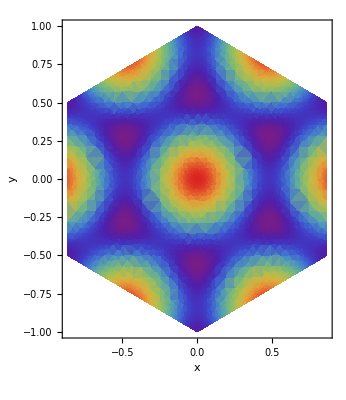

```mathematica
DensityPlot[nRnasnareauf0[x,y,10Sqrt[3],1.06],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],AspectRatio->Automatic]
```

```mathematica
t1=AbsoluteTime[];
AAhex[r_,p_]=FullSimplify[Integrate[nRnasnareauf0[x,y,r,p]Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}]/hexagonarea ]
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins"]
```

(3 (1+2 Cos[(2 (-1+p) π r)/(√3)]) Sin[((-1+p) π r)/(√3)]^2)/((-1+p)^2 π^2 r^2)

time used 1.21220477 mins

```mathematica
Import["ToMatlab.m","Package"]
```

```mathematica
ToMatlab[AAhex[r,p]]
```

3.*((-1)+p).^(-2).*pi.^(-2).*r.^(-2).*(1+2.*cos(2.*3.^(-1/2).*(( ...
  -1)+p).*pi.*r)).*sin(3.^(-1/2).*((-1)+p).*pi.*r).^2;

## AB stacking hexagon Eq.S14

```mathematica
ClearAll["Global`*"]
```

```mathematica
fAB[x_,y_,λ_]=  Cos[(4 π (x-λ/(√3)))/(√3 λ)]+2 Cos[(2  π (x-λ/(√3)))/(√3 λ)] Cos[(2  π y)/λ]
```

2 Cos[(2 π y)/λ] Cos[(2 π (x-λ/(√3)))/(√3 λ)]+Cos[(4 π (x-λ/(√3)))/(√3 λ)]

```mathematica
Plot3D[fAB[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->Automatic,ViewPoint->{0,0,Infinity}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
γ=-π/2
```

-π/2

```mathematica
λ=p as/(p-1)

(*λ is moire wavelength, distance between AA point
as is lattice constant of substrate*)
```

(as p)/(-1+p)

```mathematica
f0[x_,y_,as_,p_]=Simplify[fAB[x Cos[γ]-y Sin[γ],y Cos[γ]+x Sin[γ],λ]]
```

2 Cos[(2 (-1+p) π x)/(as p)] Sin[1/6 π (-1+(4 √3 (-1+p) y)/(as p))]+Sin[1/6 π (-5+(8 √3 (-1+p) y)/(as p))]

```mathematica
nRf0[x_,y_,as_,R_,p_]=f0[x R,y R,as,p]
```

2 Cos[(2 (-1+p) π R x)/(as p)] Sin[1/6 π (-1+(4 √3 (-1+p) R y)/(as p))]+Sin[1/6 π (-5+(8 √3 (-1+p) R y)/(as p))]

```mathematica
nRnasnareauf0[x_,y_,r_,p_]=Simplify[nRf0[x,y,as,r*as*p,p]]
```

2 Cos[2 (-1+p) π r x] Sin[1/6 π (-1+4 √3 (-1+p) r y)]+Sin[1/6 π (-5+8 √3 (-1+p) r y)]

```mathematica
hexagonarea=Integrate[Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}]
```

(3 √3)/2

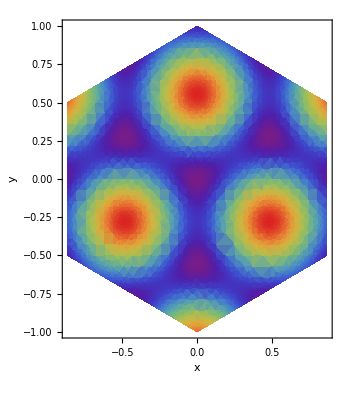

```mathematica
DensityPlot[nRnasnareauf0[x,y,10Sqrt[3],1.06],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],AspectRatio->Automatic]
```

```mathematica
t1=AbsoluteTime[];
ABhex[r_,p_]=FullSimplify[Integrate[nRnasnareauf0[x,y,r,p]Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}]/hexagonarea ]
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins"]
```

(3 (-Cos[(2 (-1+p) π r)/(√3)]+Cos[(4 (-1+p) π r)/(√3)]))/(4 (-1+p)^2 π^2 r^2)

time used 2.47277083 mins

```mathematica
ToMatlab[ABhex[r,p]]
```

(3/4).*((-1)+p).^(-2).*pi.^(-2).*r.^(-2).*((-1).*cos(2.*3.^(-1/2) ...
  .*((-1)+p).*pi.*r)+cos(4.*3.^(-1/2).*((-1)+p).*pi.*r));